# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

# Setup

```mathematica
nv=2;
nh=1;

volExp=14;
noIP3R=100;
cdir="../"<>getCacheDirRaw[volExp,noIP3R];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

# Make graphs

## Freqs

training_data_rxns/freqs.txt

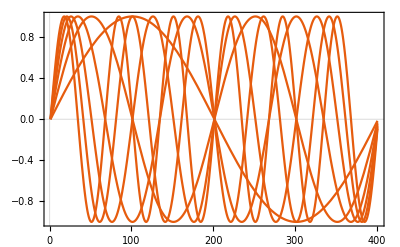

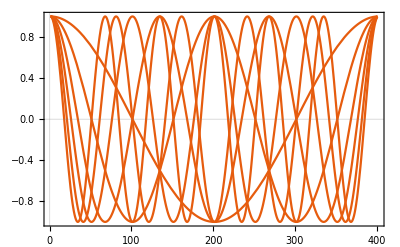

```mathematica
freqs={1,2,3,4,5,6}//N;
freqs=2*Pi/dataDesc["noTpts"]*freqs;

SetDirectory[NotebookDirectory[]];
Export["training_data_rxns/freqs.txt",freqs,"Table",Delimiter->" "]

Plot[Table[Sin[freq*(t-1)],{freq,freqs}],{t,1,dataDesc["noTpts"]}]
Plot[Table[Cos[freq*(t-1)],{freq,freqs}],{t,1,dataDesc["noTpts"]}]
```

## Rxns

```mathematica
rxnSpecs={
{"eat",1,2},
{"eat",2,1},
{"eat",1,3},
{"eat",3,1},
{"eat",2,3},
{"eat",3,2},
{"birth",1},
{"birth",2},
{"birth",3},
{"death",1},
{"death",2},
{"death",3}
};
noRxns=Length[rxnSpecs]
```

12

## Input graph without standardization

```mathematica
muhCosCoeffsInit=ConstantArray[0,Length[freqs]];
muhSinCoeffsInit=ConstantArray[0,Length[freqs]];
varhCosCoeffsInit=ConstantArray[0,Length[freqs]];
varhSinCoeffsInit=ConstantArray[0,Length[freqs]];
graphInputsWOSTD=makeGraphInputsWOSTD[nv,nh,freqs,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit,rxnSpecs];
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["training_data_rxns/graph_inputs_wo_std.wlnet",graphInputsWOSTD]
```

graph_inputs_wo_std.wlnet

## Graph for calculating STDs

```mathematica
fourier[offset_,sinCoeffs_,cosCoeffs_,freqs_,tptPlt_]:=Module[
{range,pts}
,
range=Max[Total[Abs[sinCoeffs]+Abs[cosCoeffs]]+10^-8,1];
pts=Table[offset[[1]]+(Sum[sinCoeffs[[i]]*Sin[freqs[[i]]*(tpt-1)]+cosCoeffs[[i]]*Cos[freqs[[i]]*(tpt-1)],{i,Length[freqs]}])/range,{tpt,tptPlt}];

Return[pts];
];
```

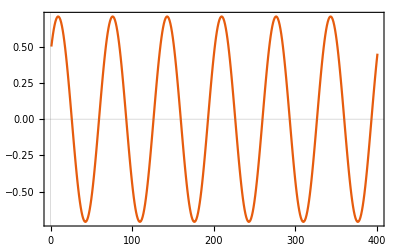
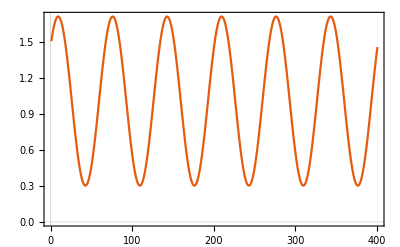

```mathematica
(* Highest freq sin + cos only *)
freqsTrial={freqs[[-1]]};
muhCosCoeffsInitTrial={1.0};
muhSinCoeffsInitTrial={1.0};
varhCosCoeffsInitTrial={1.0};
varhSinCoeffsInitTrial={1.0};

tptsTrial=Table[t,{t,1,dataDesc["noTpts"]}];
muhTrial=fourier[{0.0},muhSinCoeffsInitTrial,muhCosCoeffsInitTrial,freqsTrial,tptsTrial];
varhTrial=fourier[{1.01},varhSinCoeffsInitTrial,varhCosCoeffsInitTrial,freqsTrial,tptsTrial];

Row[{
ListLinePlot[Flatten[muhTrial]],
ListLinePlot[Flatten[varhTrial]]
}]
```

```mathematica
graphCalculateSTDs=makeGraphInputsWOSTD[nv,nh,freqsTrial,muhCosCoeffsInitTrial,muhSinCoeffsInitTrial,varhCosCoeffsInitTrial,varhSinCoeffsInitTrial,rxnSpecs];
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["training_data_rxns/graph_calculate_stds.wlnet",graphCalculateSTDs]
```

graph_calculate_stds.wlnet